## jekyll and wolf: part 3

In the gripping final chapter, we discover how elementary cellular automaton rule 22 looks when you plot the total number of black cells as a function of time step:

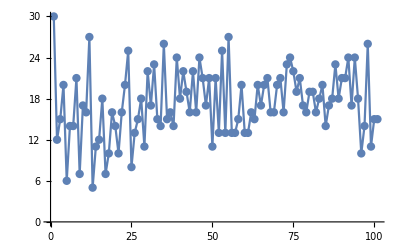

```mathematica
ListPlot[Total/@CellularAutomaton[22,RandomInteger[1,50],100],Joined->True,Mesh->All]
```